Parameters

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
boxLength=1000;
```

```mathematica
fname="../bimol_annihilation/lattice_v300/pre.txt";
```

```mathematica
importLattice[fname_]:=Module[
{latt,lattComplete},
latt=Import[fname,"Table"][[;;,1]];

	lattComplete=ConstantArray[0,boxLength];
Do[
lattComplete[[l]]=1;
,{l,latt}];

Return[lattComplete];
];
```

Visualize the lattice

```mathematica
visualizeLattice[lattice_,boxLength_,color_,left_,right_]:=Graphics[
Table[
{Blend[{White,color},lattice[[i]]],EdgeForm[Thin],Rectangle[{i,0}]}
,{i,left,right}]
,Background->White];
```

```mathematica
showColumns[latt_,nColumn_,interval_,color_]:=Column[Table[
Show[visualizeLattice[latt,boxLength,color,(i-1)*interval+1,i*interval],ImageSize->800]
,
{i,1,nColumn}
]]
```

Sample

```mathematica
sampleLatt[h_,j_,k_,boxLength_,lattIn_]:=Module[
{lattOut,act,idxs,p}
,
(* IMPORTANT: MUST overwrite the old lattice on the fly *)
lattOut=lattIn;
s=10000;

Do[
act=h;
If[ipos==s,Print[act]];

(* NN *)
If[ipos==1,idxs={2}];
If[ipos==boxLength,idxs={boxLength-1}];
If[ipos≠1&&ipos≠boxLength,idxs={ipos-1,ipos+1}];
actNN=0.0;
Do[
act+=j*lattOut[[idx]];
actNN+=j*lattOut[[idx]];
If[ipos==s,Print[idx," ",j*lattOut[[idx]]]];
,{idx,idxs}];
If[ipos==s,Print[actNN]];

(* Triplet *)
If[ipos==1,idxs={{2,3}}];
If[ipos==boxLength,idxs={{boxLength-2,boxLength-1}}];
If[ipos==2,idxs={{1,3},{3,4}}];
If[ipos==boxLength-1,idxs={{boxLength-2,boxLength},{boxLength-3,boxLength-2}}];
If[ipos!=1&&ipos≠2&&ipos≠boxLength-1&&ipos≠boxLength,idxs={{ipos-2,ipos-1},{ipos-1,ipos+1},{ipos+1,ipos+2}}];
actTriplet=0.0;
Do[
act+=k*lattOut[[idx[[1]]]]*lattOut[[idx[[2]]]];
actTriplet+=k*lattOut[[idx[[1]]]]*lattOut[[idx[[2]]]];
,{idx,idxs}];
If[ipos==s,Print[actTriplet]];

act=LogisticSigmoid[act];
(*Print[ipos," ",act];*)

(* USE PROBABILITIES! *)
(* IMPORTANT: overwrite old! *)
(*
lattOut[[ipos]]=act;
*)
If[RandomReal[{0,1}]≤act,lattOut[[ipos]]=1.0,lattOut[[ipos]]=0.0];

,{ipos,1,boxLength}];

Return[lattOut]
];
```

```mathematica
hTest=-2.99927;
jTest=0.0612041;
kTest=2.77309;
```

```mathematica
latt=importLattice[fname];
```

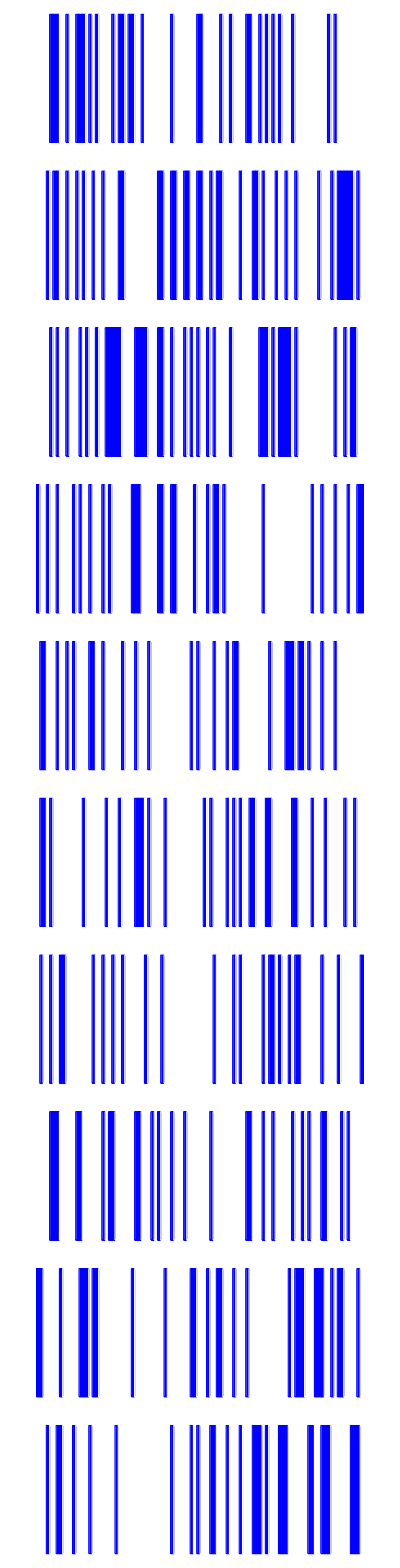

```mathematica
showColumns[latt,10,100,Blue]
```

```mathematica
lattSampled=sampleLatt[hTest,jTest,kTest,boxLength,latt];
```

-2.99927

4 0.

6 0.0612041

0.0612041

2.77309

```mathematica
lattSampled
```

Count triplets

```mathematica
countTriplets[latt_]:=Module[
{ctr,lprev,l,lnext},
ctr=0;
Do[
lprev=latt[[i-1]];
l=latt[[i]];
lnext=latt[[i+1]];

ctr+=lprev*l*lnext;
,{i,2,Length[latt]-1}];
Return[ctr];
];
```

```mathematica
lattSampled2=latt;
Do[
lattSampled2=sampleLatt[hTest,jTest,kTest,boxLength,lattSampled2];
If[Mod[i,100]==0,Print[countTriplets[lattSampled2]]];
,{i,1,1000}];
```

20.

18.

26.

41.

67.

26.

46.

21.

29.

51.

```mathematica
countTriplets[lattSampled2]
```

33.

Lattice sampled by Stoch sim

```mathematica
fnamePost="../bimol_annihilation/lattice_v300/lattice/0000.txt";
lattPost=importLattice[fnamePost];
```

```mathematica
countTriplets[lattPost]
```

29

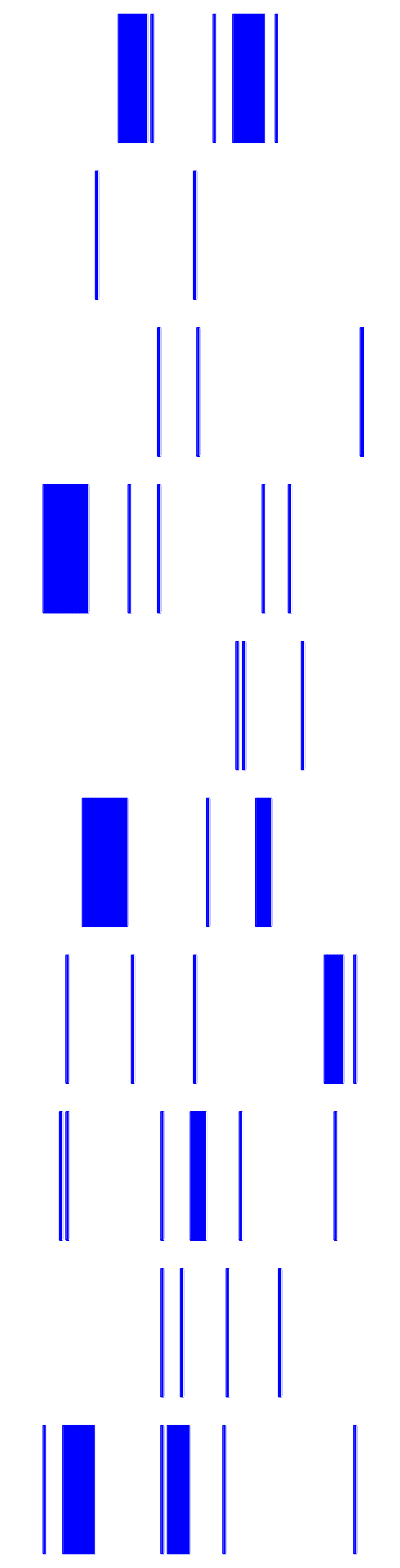

```mathematica
showColumns[lattPost,10,100,Blue]
```